Autor: Krzysztof Barczak

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 2

Metoda Adamsa-Bashfortha

Napisać procedurę realizującą algorytm trzy krokowej metody Adamsa-Bashfortha (argumenty:  f, x_0, y_0, b, n).
Zminimalizować liczbę obliczeń funkcji   f. Jako metodę startową wykorzystać metodę Rungego-Kutty rzędu trzeciego.

Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=((y(x))/x^2)^(1/3),  x∈[1,50],
y(1)=1.

Obliczenia wykonać dla 10, 20 i 50 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.

## Rozwiązanie

### Metoda Rungego-Kutty rzędu trzeciego - kod procedury

Wejście: 
	f = f(x,y) - funkcja;
	x0, y0 - wartości;
	n - liczba kroków;
	h - długość kroku.
Wyjście:
	(x_i,y_i) dla i=0,1,...,n - punkty.

```mathematica
Clear[metodaRK3];
metodaRK3[f_,x0_,y0_,h_,n_]:=Module[{yValues,xValues,xNext=x0,yNext=y0,k1,k2,k3},

xValues={x0};
yValues={y0};

Do[
k1=f[xNext,yNext];
k2=f[xNext+h/2,yNext+(h k1)/2];
xNext=xNext+h;
xValues=Append[xValues,xNext];
k3=f[xNext,yNext-h k1+2 h k2];
yNext=yNext+1/6 h (k1+4 k2+k3);
yValues=Append[yValues,yNext],
{i,0,n-1}];

Return[Transpose[{xValues,yValues}]]
]
```

### Metoda Adamsa-Bashfortha - kod procedury

Wejście:
	f - funkcja f(x, y),
	x0, y0 - wartości x_0, y_0,
	b - koniec przedziału,
	n - liczba kroków.
Wyjście:
	punkty (x_i, y_i), i = 0, 1, ..., n.

```mathematica
Clear[metodaAB];
metodaAB[f_,x0_,y0_,b_,m_]:=Module[{h=(b-x0)/m,xi,k=3,yi,fi,bki,temp=0},
xi=Table[x0+i h,{i,1,k-1}];
xi=Prepend[xi,x0];

(* Wartości Subscript[y, i] dla i = 1, ..., k-1 wyznaczone z użyciem metodaRK3 *)
yi=metodaRK3[f,x0,y0,h,k-1][[All,2]];
fi=Table[f[xi⟦i⟧,yi⟦i⟧],{i,1,k}];

bki=N[{23/12,-16/12,5/12}];

Do[
temp=yi⟦n-1⟧+h ∑_(i=1)^k bki⟦i⟧ f[xi⟦n-i⟧,yi⟦n-i⟧];
yi=Append[yi,temp];
xi=Append[xi,xi[[n-1]]+h];
fi=Append[fi,f[xi[[n]],yi[[n]]]],
{n,k+1,m+1}];

Return[Transpose[{xi,yi}]]
]
```

### Rozwiązanie zagadnienia początkowego

```mathematica
Clear[f,x0,y0,b,n];
f[x_,y_]:=(y/x^2)^(1/3);
x0=1.;y0=1.;b=50.;
przyblizone10=metodaAB[f,x0,y0,b,10];
przyblizone20=metodaAB[f,x0,y0,b,20];
przyblizone50=metodaAB[f,x0,y0,b,50];
dokladne=DSolve[{y'[x]==(y[x]/x^2)^(1/3),y[1]==1},y[x],x][[1,1,2]];
```

```mathematica
przyblizoneWykres10=ListPlot[przyblizone10,PlotLegends->{"n=10"},PlotStyle->Blue];
przyblizoneWykres20=ListPlot[przyblizone20,PlotLegends->{"n=20"},PlotStyle->Orange];
przyblizoneWykres50=ListPlot[przyblizone50,PlotLegends->{"n=50"},PlotStyle->Purple];
dokladneWykres=Plot[dokladne,{x,1,50},PlotLegends->{"dokładne"},PlotStyle->LightPurple];
```

```mathematica
Clear[h,n,wartosci];
h={(b-x0)/10,(b-x0)/20,(b-x0)/50};
n={10,20,50};
wartosci=Table[dokladne/.{x->xw},{i,1,3},{xw,x0,x0+h[[i]]*n[[i]],h[[i]]}];
```

```mathematica
bledy10=Table[{przyblizone10[[i,1]],Abs[przyblizone10[[i,2]]-wartosci[[1,i]]]},{i,Length[przyblizone10]}];
bledy20=Table[{przyblizone20[[i,1]],Abs[przyblizone20[[i,2]]-wartosci[[2,i]]]},{i,Length[przyblizone20]}];
bledy50=Table[{przyblizone50[[i,1]],Abs[przyblizone50[[i,2]]-wartosci[[3,i]]]},{i,Length[przyblizone50]}];
```

```mathematica
bledyWykres10=ListPlot[bledy10,Joined->True,PlotLegends->{"n=10"},PlotStyle->{Blue,Thickness[0.005]}];
bledyWykres20=ListPlot[bledy20,Joined->True,PlotLegends->{"n=20"},PlotStyle->{Orange,Thickness[0.005]}];
bledyWykres50=ListPlot[bledy50,Joined->True,PlotLegends->{"n=50"},PlotStyle->{Purple,Thickness[0.005]}];
```

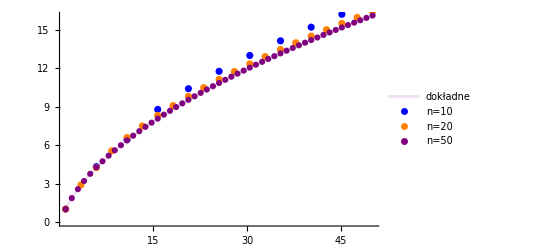

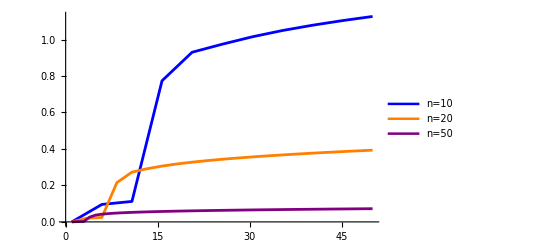

```mathematica
Show[dokladneWykres,przyblizoneWykres10,przyblizoneWykres20,przyblizoneWykres50]
Show[bledyWykres10,bledyWykres20,bledyWykres50]
```